```mathematica
Clear["Global`*"]
```

## Define the rate laws and the steady state equations

```mathematica
ff[1]=(Subscript[x, 0]-Subscript[x, 1])/(Subscript[a, 1] Subscript[x, 0]+Subscript[b, 1] Subscript[x, 1] + Subscript[c, 1]);
ff[2]=(Subscript[x, 1])/(Subscript[a, 2] Subscript[x, 1] + Subscript[c, 2]);

F1=e1 f1[x1[e1,e2]]-c[e1,e2];
F2=e2 f2[x1[e1,e2]]-c[e1,e2];

n=1;
kineticsrules = 
Flatten[Append[Table[Subscript[f, i]->ff[i],{i,1,n+1}],Flatten[Table[Table[Subscript[f, i,j]-> D[ff[i],Subscript[x, j]],{j,1,n}],{i,1,n+1}]]]]
```

{f_1→(x_0-x_1)/(c_1+a_1 x_0+b_1 x_1),f_2→x_1/(c_2+a_2 x_1),f_(1,1)→-(b_1 (x_0-x_1))/(c_1+a_1 x_0+b_1 x_1)^2-1/(c_1+a_1 x_0+b_1 x_1),f_(2,1)→-(a_2 x_1)/(c_2+a_2 x_1)^2+1/(c_2+a_2 x_1)}

## A list of replacement rules

```mathematica
enzrules={e1->C/Subscript[f, 1],e2->c/Subscript[f, 2]};
xxi={Subscript[x, 0]->Subscript[ξ, 0],Subscript[x, 1]->Subscript[ξ, 1]};
crule={C->1/(1/Subscript[f, 1] + 1/Subscript[f, 2] )};
frules={
f1[x1[e1,e2]]->Subscript[f, 1],
f2[x1[e1,e2]]->Subscript[f, 2],

f1'[x1[e1,e2]]->Subscript[f, 1,1],
f2'[x1[e1,e2]]->Subscript[f, 2,1]
};
```

## Compute the first order partial derivatives along the QSS surface, using x1=x1[e1,e2], c=c[e1,e2].

```mathematica
derivsNis2=Solve[{
D[F1,e1]==0,
D[F1,e2]==0,
D[F2,e1]==0,
D[F2,e2]==0
},
{Derivative[1,0][x1][e1,e2] ,
Derivative[0,1][x1][e1,e2],
Derivative[1,0][c][e1,e2],
Derivative[0,1][c][e1,e2]
}];
```

## This is dx1/de along the Quasi Steady State

```mathematica
dx1de={Derivative[1,0][x1][e1,e2],Derivative[0,1][x1][e1,e2]}/. derivsNis2;
dx1de=dx1de/.frules(**/.enzrules/.crule/.frules//Simplify**)
```

{{-f_1/(e1 f_(1,1)-e2 f_(2,1)),f_2/(e1 f_(1,1)-e2 f_(2,1))}}

```mathematica
Subscript[ϵ, 1]=1/Subscript[f, 1]/.kineticsrules/.xxi;
Subscript[ϵ, 2]=1/Subscript[f, 2]/.kineticsrules/.xxi;
som=(1/Subscript[f, 1]+1/Subscript[f, 2])/.kineticsrules/.xxi
Eqs=({D[som,Subscript[ξ, 1]]==0}//Simplify)/.{Subscript[ξ, 0]-> Subscript[ξ, 0][Subscript[ξ, 1]]}
dxidx1=Solve[D[Eqs,Subscript[ξ, 1]],{Subscript[ξ, 0]'[Subscript[ξ, 1]]}]
```

(c_2+a_2 ξ_1)/ξ_1+(c_1+a_1 ξ_0+b_1 ξ_1)/(ξ_0-ξ_1)

{(c_1+(a_1+b_1) ξ_0[ξ_1])/(-ξ_1+ξ_0[ξ_1])^2==c_2/ξ_1^2}

{{ξ_0'[ξ_1]→(-(2 c_2)/ξ_1^3-(2 (c_1+(a_1+b_1) ξ_0[ξ_1]))/(-ξ_1+ξ_0[ξ_1])^3)/((a_1+b_1)/(-ξ_1+ξ_0[ξ_1])^2-(2 (c_1+(a_1+b_1) ξ_0[ξ_1]))/(-ξ_1+ξ_0[ξ_1])^3)}}

```mathematica
posx= {Subscript[x, 0]->Subscript[y, 0]+ Subscript[x, 1]};
posxi= {Subscript[ξ, 0]-> Subscript[η, 0]+Subscript[ξ, 1]};
Deps1Dxi0Dx1=(D[Subscript[ϵ, 1],Subscript[ξ, 0]]Subscript[ξ, 0]'[Subscript[ξ, 1]])/.dxidx1 /.{Subscript[ξ, 0][Subscript[ξ, 1]]->Subscript[ξ, 0]}/.posxi//Factor//Simplify
Deps1Dx1=(D[Subscript[ϵ, 1],Subscript[ξ, 1]])/.posxi//Factor
DX1DE1=dx1de[[1]][[1]]/.kineticsrules/.posx//Factor;
DX1DE2=dx1de[[1]][[2]]/.kineticsrules/.posx//Factor;
TraceEps=(Deps1Dxi0Dx1 DX1DE1 + Deps1Dx1 (DX1DE1 - DX1DE2) )/.{Subscript[ξ, 1]->Subscript[x, 1]};
TraceEps=TraceEps/.enzrules/.crule/.kineticsrules/.posx//Factor
```

{-(2 (c_1+(a_1+b_1) ξ_1) (c_2 η_0^3+ξ_1^3 (c_1+(a_1+b_1) (η_0+ξ_1))))/(η_0^2 ξ_1^3 (2 c_1+(a_1+b_1) (η_0+2 ξ_1)))}

(c_1+a_1 η_0+b_1 η_0+a_1 ξ_1+b_1 ξ_1)/η_0^2

{-(((c_1 x_1+a_1 x_1^2+b_1 x_1^2+c_2 y_0+a_1 x_1 y_0+a_2 x_1 y_0) (-2 c_1^3 x_1^4-6 a_1 c_1^2 x_1^5-6 b_1 c_1^2 x_1^5-6 a_1^2 c_1 x_1^6-12 a_1 b_1 c_1 x_1^6-6 b_1^2 c_1 x_1^6-2 a_1^3 x_1^7-6 a_1^2 b_1 x_1^7-6 a_1 b_1^2 x_1^7-2 b_1^3 x_1^7-2 a_1 c_1^2 x_1^4 y_0-4 a_1^2 c_1 x_1^5 y_0-4 a_1 b_1 c_1 x_1^5 y_0-2 a_1^3 x_1^6 y_0-4 a_1^2 b_1 x_1^6 y_0-2 a_1 b_1^2 x_1^6 y_0-3 a_1 c_1^2 x_1^4 η_0-3 b_1 c_1^2 x_1^4 η_0-6 a_1^2 c_1 x_1^5 η_0-12 a_1 b_1 c_1 x_1^5 η_0-6 b_1^2 c_1 x_1^5 η_0-3 a_1^3 x_1^6 η_0-9 a_1^2 b_1 x_1^6 η_0-9 a_1 b_1^2 x_1^6 η_0-3 b_1^3 x_1^6 η_0-a_1 c_1 c_2 x_1^3 y_0 η_0-b_1 c_1 c_2 x_1^3 y_0 η_0-3 a_1^2 c_1 x_1^4 y_0 η_0-a_1 a_2 c_1 x_1^4 y_0 η_0-3 a_1 b_1 c_1 x_1^4 y_0 η_0-a_2 b_1 c_1 x_1^4 y_0 η_0-a_1^2 c_2 x_1^4 y_0 η_0-2 a_1 b_1 c_2 x_1^4 y_0 η_0-b_1^2 c_2 x_1^4 y_0 η_0-3 a_1^3 x_1^5 y_0 η_0-a_1^2 a_2 x_1^5 y_0 η_0-6 a_1^2 b_1 x_1^5 y_0 η_0-2 a_1 a_2 b_1 x_1^5 y_0 η_0-3 a_1 b_1^2 x_1^5 y_0 η_0-a_2 b_1^2 x_1^5 y_0 η_0-a_1^2 c_1 x_1^4 η_0^2-2 a_1 b_1 c_1 x_1^4 η_0^2-b_1^2 c_1 x_1^4 η_0^2-a_1^3 x_1^5 η_0^2-3 a_1^2 b_1 x_1^5 η_0^2-3 a_1 b_1^2 x_1^5 η_0^2-b_1^3 x_1^5 η_0^2-a_1^2 c_2 x_1^3 y_0 η_0^2-2 a_1 b_1 c_2 x_1^3 y_0 η_0^2-b_1^2 c_2 x_1^3 y_0 η_0^2-a_1^3 x_1^4 y_0 η_0^2-a_1^2 a_2 x_1^4 y_0 η_0^2-2 a_1^2 b_1 x_1^4 y_0 η_0^2-2 a_1 a_2 b_1 x_1^4 y_0 η_0^2-a_1 b_1^2 x_1^4 y_0 η_0^2-a_2 b_1^2 x_1^4 y_0 η_0^2+2 c_1 c_2^2 y_0 η_0^3+2 a_2 c_1 c_2 x_1 y_0 η_0^3+2 a_1 c_2^2 x_1 y_0 η_0^3+2 b_1 c_2^2 x_1 y_0 η_0^3+2 a_1 a_2 c_2 x_1^2 y_0 η_0^3+2 a_2 b_1 c_2 x_1^2 y_0 η_0^3))/(x_1^2 (c c_1^2 c_2 x_1+c_1 c_2 x_1^2+2 c a_1 c_1 c_2 x_1^2+2 c b_1 c_1 c_2 x_1^2+a_2 c_1 x_1^3+a_1 c_2 x_1^3+c a_1^2 c_2 x_1^3+b_1 c_2 x_1^3+2 c a_1 b_1 c_2 x_1^3+c b_1^2 c_2 x_1^3+a_1 a_2 x_1^4+a_2 b_1 x_1^4+c c_1 c_2^2 y_0+2 c a_1 c_1 c_2 x_1 y_0+c a_2 c_1 c_2 x_1 y_0+c a_1 c_2^2 x_1 y_0+c b_1 c_2^2 x_1 y_0+a_1 c_2 x_1^2 y_0+2 c a_1^2 c_2 x_1^2 y_0+c a_1 a_2 c_2 x_1^2 y_0+b_1 c_2 x_1^2 y_0+2 c a_1 b_1 c_2 x_1^2 y_0+c a_2 b_1 c_2 x_1^2 y_0+a_1 a_2 x_1^3 y_0+a_2 b_1 x_1^3 y_0+c a_1 c_2^2 y_0^2+c a_1^2 c_2 x_1 y_0^2+c a_1 a_2 c_2 x_1 y_0^2) η_0^2 (2 c_1+2 a_1 x_1+2 b_1 x_1+a_1 η_0+b_1 η_0)))}

```mathematica
xi0sols=Solve[Eqs/.{Subscript[ξ, 0][Subscript[ξ, 1]]-> Subscript[ξ, 0]},{Subscript[ξ, 0]}]//Simplify
```

{{ξ_0→(2 c_2 ξ_1+a_1 ξ_1^2+b_1 ξ_1^2-√(ξ_1^2 (4 c_1 c_2+(a_1+b_1) ξ_1 (4 c_2+(a_1+b_1) ξ_1))))/(2 c_2)},{ξ_0→(2 c_2 ξ_1+a_1 ξ_1^2+b_1 ξ_1^2+√(ξ_1^2 (4 c_1 c_2+(a_1+b_1) ξ_1 (4 c_2+(a_1+b_1) ξ_1))))/(2 c_2)}}

```mathematica
TraceEps=(Deps1Dxi0Dx1 DX1DE1 + Deps1Dx1 (DX1DE1 - DX1DE2) )/.{Subscript[ξ, 1]->Subscript[x, 1]};
TraceEps=TraceEps/.enzrules/.crule/.kineticsrules/.{Subscript[η, 0]->Subscript[ξ, 0]-Subscript[x, 1]}/.xi0sols[[1]]/.{Subscript[ξ, 1]->Subscript[x, 1]}
```

{(2 (c_1+(a_1+b_1) x_1) (c_2 (-x_1+(2 c_2 x_1+a_1 x_1^2+b_1 x_1^2-√(x_1^2 (4 c_1 c_2+(a_1+b_1) x_1 (4 c_2+(a_1+b_1) x_1))))/(2 c_2))^3+x_1^3 (c_1+((a_1+b_1) (2 c_2 x_1+a_1 x_1^2+b_1 x_1^2-√(x_1^2 (4 c_1 c_2+(a_1+b_1) x_1 (4 c_2+(a_1+b_1) x_1)))))/(2 c_2))) y_0)/(x_1^3 (-x_1+(2 c_2 x_1+a_1 x_1^2+b_1 x_1^2-√(x_1^2 (4 c_1 c_2+(a_1+b_1) x_1 (4 c_2+(a_1+b_1) x_1))))/(2 c_2))^2 (2 c_1+(a_1+b_1) (x_1+(2 c_2 x_1+a_1 x_1^2+b_1 x_1^2-√(x_1^2 (4 c_1 c_2+(a_1+b_1) x_1 (4 c_2+(a_1+b_1) x_1))))/(2 c_2))) (c_1+a_1 x_1+b_1 x_1+a_1 y_0))+((c_1+a_1 x_1+b_1 x_1+a_1 (-x_1+(2 c_2 x_1+a_1 x_1^2+b_1 x_1^2-√(x_1^2 (4 c_1 c_2+(a_1+b_1) x_1 (4 c_2+(a_1+b_1) x_1))))/(2 c_2))+b_1 (-x_1+(2 c_2 x_1+a_1 x_1^2+b_1 x_1^2-√(x_1^2 (4 c_1 c_2+(a_1+b_1) x_1 (4 c_2+(a_1+b_1) x_1))))/(2 c_2))) (-x_1/(c_2+a_2 x_1)-y_0/(c_1+a_1 x_1+b_1 x_1+a_1 y_0)))/(-x_1+(2 c_2 x_1+a_1 x_1^2+b_1 x_1^2-√(x_1^2 (4 c_1 c_2+(a_1+b_1) x_1 (4 c_2+(a_1+b_1) x_1))))/(2 c_2))^2}

{a_1→1,b_1→2,c_1→3,a_2→2,b_2→2,c_2→3,c_3→5,a_3→1,b_3→2,y_0→1}

{((-x_1/(3+2 x_1)-1/(4+3 x_1)) (3+2 x_1+1/6 (6 x_1+3 x_1^2-√(x_1^2 (36+3 x_1 (12+3 x_1))))+2 (-x_1+1/6 (6 x_1+3 x_1^2-√(x_1^2 (36+3 x_1 (12+3 x_1)))))))/(-x_1+1/6 (6 x_1+3 x_1^2-√(x_1^2 (36+3 x_1 (12+3 x_1)))))^2+(2 (3+3 x_1) (3 (-x_1+1/6 (6 x_1+3 x_1^2-√(x_1^2 (36+3 x_1 (12+3 x_1)))))^3+x_1^3 (3+1/2 (6 x_1+3 x_1^2-√(x_1^2 (36+3 x_1 (12+3 x_1)))))))/(x_1^3 (4+3 x_1) (-x_1+1/6 (6 x_1+3 x_1^2-√(x_1^2 (36+3 x_1 (12+3 x_1)))))^2 (6+3 (x_1+1/6 (6 x_1+3 x_1^2-√(x_1^2 (36+3 x_1 (12+3 x_1)))))))}

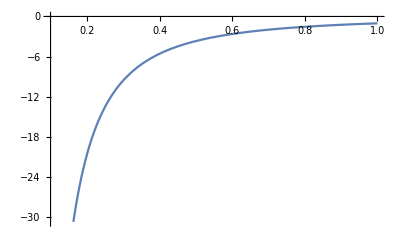

```mathematica
pars={Subscript[a, 1]->1,Subscript[b, 1]->2,Subscript[c, 1]->3,
Subscript[a, 2]->2,Subscript[b, 2]->2,Subscript[c, 2]->3,Subscript[c, 3]->5,
Subscript[a, 3]->1,Subscript[b, 3]->2,Subscript[y, 0]->1}
TraceEps/.pars
Plot[TraceEps/.pars,{Subscript[x, 1],0.1,1}]
```

```mathematica
TraceEps//FullSimplify
```

{5287751643588552171/2407062268370000}

```mathematica
t=TraceEps
```

{(((e3 c_3 11(c_2+1+1+a_2 y_1) (1)^2)/(e2 e3 c_1^2 c_2 c_3+213+e1 e3 a_1 a_2^2 c_3 K_1^2 y_1^3)+1) 1)/η_0^2+1/1-(y_0 3 (4 b_1 c_3 K_1 η_0 η_1^4+34+4 c_2 η_1 (1)))/(2 (1) 2 (1) (c_3 η_1^3+K_2 ξ_2^3 (c_2 K_2+1)))}
 |  |  |  |

```mathematica
Denominator[t]
```

{1}

```mathematica
posneg[expr_]:=Values@GroupBy[Replace[expr,{a_Plus:>List@@a,a_:>{a}}],Internal`SyntacticNegativeQ,Total]
td=Numerator[t]//Expand;
pp=posneg[Expand[Numerator[t]]][[1]];
ppn=posneg[pp[[1]]];
```

```mathematica
Numerator[t]
```

{-(c_1+b_1 K_2 x_2+a_1 K_1 K_2 x_2+a_1 y_0+b_1 y_1+a_1 K_1 y_1) (e2 b_2^2 c_1 c_2^2 c_3 K_2^2 x_2^4 y_0^5+2 e2 a_2 b_2 c_1 c_2^2 c_3 K_2^3 x_2^4 y_0^5+e2 a_2^2 c_1 c_2^2 c_3 K_2^4 x_2^4 y_0^5+e2 a_3 b_2^2 c_1 c_2^2 K_2^2 x_2^5 y_0^5+2 e2 b_2^3 c_1 c_2 c_3 K_2^2 x_2^5 y_0^5+2 e2 a_2 a_3 b_2 c_1 c_2^2 K_2^3 x_2^5 y_0^5+6 e2 a_2 b_2^2 c_1 c_2 c_3 K_2^3 x_2^5 y_0^5+e2 b_1 b_2^2 c_2^2 c_3 K_2^3 x_2^5 y_0^5+e2 a_1 b_2^2 c_2^2 c_3 K_1 K_2^3 x_2^5 y_0^5+e2 a_2^2 a_3 c_1 c_2^2 K_2^4 x_2^5 y_0^5+6 e2 a_2^2 b_2 c_1 c_2 c_3 K_2^4 x_2^5 y_0^5+2 e2 a_2 b_1 b_2 c_2^2 c_3 K_2^4 x_2^5 y_0^5+2 e2 a_1 a_2 b_2 c_2^2 c_3 K_1 K_2^4 x_2^5 y_0^5+2 e2 a_2^3 c_1 c_2 c_3 K_2^5 x_2^5 y_0^5+e2 a_2^2 b_1 c_2^2 c_3 K_2^5 x_2^5 y_0^5+e2 a_1 a_2^2 c_2^2 c_3 K_1 K_2^5 x_2^5 y_0^5+2 e2 a_3 b_2^3 c_1 c_2 K_2^2 x_2^6 y_0^5+e2 b_2^4 c_1 c_3 K_2^2 x_2^6 y_0^5+6 e2 a_2 a_3 b_2^2 c_1 c_2 K_2^3 x_2^6 y_0^5+e2 a_3 b_1 b_2^2 c_2^2 K_2^3 x_2^6 y_0^5+4 e2 a_2 b_2^3 c_1 c_3 K_2^3 x_2^6 y_0^5+2 e2 b_1 b_2^3 c_2 c_3 K_2^3 x_2^6 y_0^5+e2 a_1 a_3 b_2^2 c_2^2 K_1 K_2^3 x_2^6 y_0^5+2 e2 a_1 b_2^3 c_2 c_3 K_1 K_2^3 x_2^6 y_0^5+6 e2 a_2^2 a_3 b_2 c_1 c_2 K_2^4 x_2^6 y_0^5+2 e2 a_2 a_3 b_1 b_2 c_2^2 K_2^4 x_2^6 y_0^5+6 e2 a_2^2 b_2^2 c_1 c_3 K_2^4 x_2^6 y_0^5+6 e2 a_2 b_1 b_2^2 c_2 c_3 K_2^4 x_2^6 y_0^5+2 e2 a_1 a_2 a_3 b_2 c_2^2 K_1 K_2^4 x_2^6 y_0^5+6 e2 a_1 a_2 b_2^2 c_2 c_3 K_1 K_2^4 x_2^6 y_0^5+2 e2 a_2^3 a_3 c_1 c_2 K_2^5 x_2^6 y_0^5+e2 a_2^2 a_3 b_1 c_2^2 K_2^5 x_2^6 y_0^5+4 e2 a_2^3 b_2 c_1 c_3 K_2^5 x_2^6 y_0^5+6 e2 a_2^2 b_1 b_2 c_2 c_3 K_2^5 x_2^6 y_0^5+e2 a_1 a_2^2 a_3 c_2^2 K_1 K_2^5 x_2^6 y_0^5+6 e2 a_1 a_2^2 b_2 c_2 c_3 K_1 K_2^5 x_2^6 y_0^5+e2 a_2^4 c_1 c_3 K_2^6 x_2^6 y_0^5+2 e2 a_2^3 b_1 c_2 c_3 K_2^6 x_2^6 y_0^5+2 e2 a_1 a_2^3 c_2 c_3 K_1 K_2^6 x_2^6 y_0^5+e2 a_3 b_2^4 c_1 K_2^2 x_2^7 y_0^5+4 e2 a_2 a_3 b_2^3 c_1 K_2^3 x_2^7 y_0^5+2 e2 a_3 b_1 b_2^3 c_2 K_2^3 x_2^7 y_0^5+8768+4 e3 a_2 b_1^2 b_2 c_3^2 K_1^2 y_0^2 y_1^9-8 e3 a_1^3 a_2 c_3^2 K_1^3 y_0^2 y_1^9-2 e3 a_1^2 a_2^2 c_3^2 K_1^3 y_0^2 y_1^9+8 e3 a_1 a_2 b_1 b_2 c_3^2 K_1^3 y_0^2 y_1^9+4 e3 a_1^2 a_2 b_2 c_3^2 K_1^4 y_0^2 y_1^9+4 e3 a_2^2 b_1^2 c_3^2 K_1^2 K_2 y_0^2 y_1^9+8 e3 a_1 a_2^2 b_1 c_3^2 K_1^3 K_2 y_0^2 y_1^9+4 e3 a_1^2 a_2^2 c_3^2 K_1^4 K_2 y_0^2 y_1^9-12 e3 a_2 b_1^2 c_1 c_3^2 K_1^2 y_1^10-4 e3 b_1^3 c_2 c_3^2 K_1^2 y_1^10-24 e3 a_1 a_2 b_1 c_1 c_3^2 K_1^3 y_1^10-12 e3 a_1 b_1^2 c_2 c_3^2 K_1^3 y_1^10-12 e3 a_1^2 a_2 c_1 c_3^2 K_1^4 y_1^10-12 e3 a_1^2 b_1 c_2 c_3^2 K_1^4 y_1^10-4 e3 a_1^3 c_2 c_3^2 K_1^5 y_1^10-4 e3 b_1^3 b_2 c_3^2 K_1^2 x_2 y_1^10-12 e3 a_1 b_1^2 b_2 c_3^2 K_1^3 x_2 y_1^10-12 e3 a_1^2 b_1 b_2 c_3^2 K_1^4 x_2 y_1^10-4 e3 a_1^3 b_2 c_3^2 K_1^5 x_2 y_1^10-16 e3 a_2 b_1^3 c_3^2 K_1^2 K_2 x_2 y_1^10-48 e3 a_1 a_2 b_1^2 c_3^2 K_1^3 K_2 x_2 y_1^10-48 e3 a_1^2 a_2 b_1 c_3^2 K_1^4 K_2 x_2 y_1^10-16 e3 a_1^3 a_2 c_3^2 K_1^5 K_2 x_2 y_1^10-6 e3 a_2 b_1^3 c_3^2 K_1 y_0 y_1^10-22 e3 a_1 a_2 b_1^2 c_3^2 K_1^2 y_0 y_1^10-26 e3 a_1^2 a_2 b_1 c_3^2 K_1^3 y_0 y_1^10-10 e3 a_1^3 a_2 c_3^2 K_1^4 y_0 y_1^10-4 e3 a_2 b_1^3 c_3^2 K_1^2 y_1^11-12 e3 a_1 a_2 b_1^2 c_3^2 K_1^3 y_1^11-12 e3 a_1^2 a_2 b_1 c_3^2 K_1^4 y_1^11-4 e3 a_1^3 a_2 c_3^2 K_1^5 y_1^11)}
 |  |  |  |

```mathematica
Deps1Dxi0Dx1/Deps1Dx1
DX1DE1/DX1DE2
```

{-(2 (c_1+(a_1+b_1) ξ_1) (c_2 η_0^3+ξ_1^3 (c_1+(a_1+b_1) (η_0+ξ_1))))/(ξ_1^3 (c_1+a_1 η_0+b_1 η_0+a_1 ξ_1+b_1 ξ_1) (2 c_1+(a_1+b_1) (η_0+2 ξ_1)))}

-((c_2+a_2 x_1) y_0)/(x_1 (c_1+a_1 x_1+b_1 x_1+a_1 y_0))

```mathematica
Sqrt[239.5^2 + 4.5^2]
```

239.542